```mathematica
Experiments with the Chua's Circuit

(*
==Chua's circuit==
the double-scroll attractor (sometimes known as Chua's attractor) is a strange attractor observed from a physical electronic chaotic circuit (generally,Chua's circuit) with a single nonlinear resistor (see Chua's Diode).The double-scroll system is often described by a system of three nonlinear ordinary differential equations and a 3-segment piecewise-linear equation (see Chua's equations).This makes the system easily simulated numerically and easily manifested physically due to Chua's circuits' simple design.
-http://www.chuacircuits.com/
-https://en.wikipedia.org/wiki/Multiscroll_attractor
dx/dt=c1*(y-x-f(x)) // m0: slope in outer region
   dy/dt=c2*(x-y+z)    // m1: slope in inner region
   dz/dt=-c3*y         // b: Breakpoints
   f(x)=m1*x+(m0-m1)/2*(|x+1|-|x-1|)
*)
```

Circuit Experiments s the with Chua'

```mathematica
hardLim[x_]:=Piecewise[{{0,x>limitValue},{1,x≤limitValue}}]; (* A hard limiter using a piecewise function *)
softLim[x_]:=(1/2)*(Tanh[ (limitValue-x)/softness]+1); (* A soft limiter using a tanh *)

(*Define the chua circuit's differential equations *)
g[x_] := m0 * x + (m1-m0)/2 * (Abs[x+b]-Abs[x-b]);
f[{x_,y_,z_}]:={c1 * (y-x-g[x]),c2*(x-y+z),-c3*y limiter[x]};

(*RK4 Runge Kutta method based on: 
https://en.wikipedia.org/wiki/Runge%E2%80%93Kutta_methods*)
h = 0.001;
RK4 := Module[{y}, 
k1 = h*f[x];
k2 = h*f[x+k1/2];
k3=h*f[x+k2/2];
k4=h*f[x+k3];
y=x+1/6*(k1+2*k2+2*k3+k4);
x = y;
Return[x]];

RK6 := Module[{y}, 
k1 = h*f[x];
k2 = h*f[x+k1/4];
k3=h*f[x+(3.0/32.0)*k1+(9.0/32.0)*k2];
k4=h*f[x+(1932.0/2197.0)*k1-(7200.0/2197.0)*k2
+(7296.0/2197.0)*k3];
k5 = h *f[x+(439.0/216.0)*k1-8.0*k2+(3680.0/513.0)*k3
-(845.0/4104.0)*k4];
k6 = h * f[x-(8.0/27.0)*k1+2.0*k2-(3544.0/2565.0)*k3
+(1859.0/4104.0)*k4-(11.0/40.0)*k5];
y=x+(16.0/135.0)*k1+(6656.0/12825.0)*k3
+(28561.0/56430.0)*k4-(9.0/50.0)*k5+(2.0/55.0)*k6;
x = y;
Return[x]];

x ={-1.5,0,0};
c1=15.6;
c2 =1;
c3 = 28;
m0=-0.714; (*slope in outer region default:-0.714 *)
m1 = -1.143; (*slope in inner region /default: -1.143 *)
b =1; (*Breakpoints *)

limiter = softLim; (* Choose the softlimiter *)
limitValue =1.83;
	(* 
	 1.83 / Period 1 limit cycle /
2.15 / High period limit cycle (!) /
2.183 / Period 2 limit cycle /
2.1995 / Period 3 limit cycle /
2.205/ Period 4 limit cycle /
2.206 / Period 5 limit cycle /
2.207 / Period 6 limit cycle /
2.208 / Period 7 limit cycle /
2.2101 / Period 8 limit cycle /
2.2105 / Period 9 limit cycle /
2.211 / Period 11 limit cycle /
2.215/ Period 24 limit cycle /
2.28-2.4 High period limit cycle/ Chaos /
 2.4-3.19/Chaos /
	>3.19/ not limited /
*)
softness = 0.13; (* Softness 0.1 very hard limiter // 0.13 boundary to hard limiter // 0.15 soft limiter  // 1 very soft limiter // 1.88 soft limiter *)

n = 45000;
chuaPlot=Table[RK6,{i,1,n}]; (* Choose the integration method RK4 or RK6 *)

(* Plot limits*)
limPlot = chuaPlot;

lims = limiter[{chuaPlot[[All,1]]}];
limPlot[[All,3]]= Flatten[Transpose[lims]];

Graphics3D[Point[chuaPlot[[All,1;;3]],VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@limPlot[[All,3]]],Axes->True,AxesLabel->{"x","y","z"},ImageSize->Large,BoxRatios->{1,1,1/GoldenRatio}]
```

-Graphics3D-

```mathematica
limitValue=3.19;
softLim[2.2417]
```

1.

0.13 Limiter plot

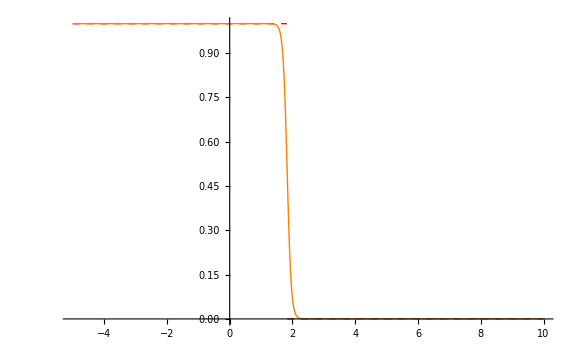

```mathematica
Limiter softness plot
softness = 0.13;
Show[Plot[hardLim[x],{x,-5,10},PlotStyle->{Red,Dashed,Thick}],Plot[softLim[x],{x,-5,10},PlotStyle->{Orange,Thick}],ImageSize->Large]
```

```mathematica
(*ModelLeg, 0g*)
SetDirectory[NotebookDirectory[]];
chuaData0g = Import["ChuaCircuit-modelLeg-0g-100s.tsv","Data"];
chuaTitle0g = chuaData0g[[1,All]];
chuaPlot0g = Drop[chuaData0g,1];

Show[ListPointPlot3D[{chuaPlot0g},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot0g}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle0g]
```

-Graphics3D-

```mathematica
(*ModelLeg, 1g*)
SetDirectory[NotebookDirectory[]];
chuaData1g = Import["ChuaCircuit-modelLeg-1g-100s.tsv","Data"];
chuaTitle1g = chuaData1g[[1,All]];
chuaPlot1g = Drop[chuaData1g,1];

Show[ListPointPlot3D[{chuaPlot1g},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g]
```

-Graphics3D-

```mathematica
(*ModelLeg, 1g,without friction, force 1*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-1g-100s-friction00.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*ModelLeg, 1g,friction 1,1,force 5*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-1g-100s-friction11-force5.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*ModelLeg, 1g,friction 1,1,force 2*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-1g-100s-friction11-force2.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*ModelLeg, 0g,friction 1,1,force 0.7,damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction11-force07-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*ModelLeg, 1g,friction 1,1,force 0.7,damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-1g-100s-friction11-force07-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*ModelLeg, 0g,friction 1,1,force 0.7,(x)yz,damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction11-force07-(x)yz-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*ModelLeg, 0g,friction 1,1,force 4,(x)yz,damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction11-force4-(x)yz-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*ModelLeg,0g, friction 0 0, force 0.7,(x)(y)z,damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction00-force07-(x)(y)z-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

-Graphics3D-

```mathematica
(*ModelLeg,0g, friction 0 0, force 0.7,xyz0.7,damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction00-force07-xyz07-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*ModelLeg,0g, friction 0 0, force 0.7,(x)yz0.7,damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction00-force07-(x)yz07-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*ModelLeg,0g, friction 0 0, force 10,(x)yz0.7,damping 0.05*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction00-force10-(x)yz07-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*ModelLeg,0g, friction 0 0, force 20,(x)yz0.7,damping 5*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction00-force20-(x)yz07-damping5.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*ModelLeg,0g, friction 0 0, force 0.7,(x)-1.5(y)z,damping 5*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction00-force07-(x)(y)z-damping5.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*ModelLeg,0g, friction 0 0, force 0.7,(x)(y)-0.5z,damping 0.5*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s,friction00-force07-(x)(y)z-damping05.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*ModelLeg, 1g,friction 1,1,force 1, xzy*)
SetDirectory[NotebookDirectory[]];
chuaData1g0 = Import["ChuaCircuit-modelLeg-0g-100s-friction11-force07-(x)yz-damping005.tsv","Data"];
chuaTitle1g0 = chuaData1g0[[1,All]];
chuaPlot1g0 = Drop[chuaData1g0,1];

Show[ListPointPlot3D[{chuaPlot1g0},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1g0}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1g0]
```

-Graphics3D-

```mathematica
(*Creature,1g, friction 2 2, force 3*10^-9*mass^2+0.02*mass,xyz,damping [1.0-0.001]*)
SetDirectory[NotebookDirectory[]];
chuaData1 = Import["c1/logChaosLogger0xbbc8700.tsv","Data"]; (*1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbc8840.tsv","Data"];*) (*similar to 1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbc83f0.tsv","Data"];*) (*similar to 1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbc9f50.tsv","Data"];*) (*similar to 1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbca090.tsv","Data"];*) (*similar to 1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbc9d30.tsv","Data"];*) (*similar to 1*)
chuaData2 = Import["c1/logChaosLogger0xbbc6bf0.tsv","Data"]; (*2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc5060.tsv","Data"]; *)(*similar to 2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc6d30.tsv","Data"]; *) (*similar to 2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc51a0.tsv","Data"];*) (*similar to 2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc4d20.tsv","Data"];*) (*similar to 2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc68b0.tsv","Data"]; *) (*similar to 2 *)

chuaData3 = Import["c2/logChaosLogger0xbbf2b80.tsv","Data"]; (*3*)
(*chuaData3 = Import["c2/logChaosLogger0xbbf2e90.tsv","Data"]; *) (*similar to 3*)
(*chuaData3 = Import["c2/logChaosLogger0xbbfbce0.tsv","Data"];*) (*simular to 3 Strong limit cycle*)
(*chuaData3 = Import["c2/logChaosLogger0xbbfbee0.tsv","Data"];*) (*simular to 3 Strong limit cycle*)
(*chuaData3 = Import["c2/logChaosLogger0xbbf2fd0.tsv","Data"];*) (*similar to 3*)
chuaData4 = Import["c2/logChaosLogger0xbbf9ee0.tsv","Data"]; (*4*)
(*chuaData3 = Import["c2/logChaosLogger0xbbfc020.tsv","Data"]; *) (*similar to 3*)
(*chuaData4 = Import["c2/logChaosLogger0xbbfa1b0.tsv","Data"]; *) (*simular to 4*)
chuaData5 = Import["c2/logChaosLogger0xbbf81e0.tsv","Data"]; (*5*)
(*chuaData5 = Import["c2/logChaosLogger0xbbf8480.tsv","Data"]; *) (*similar to 5*)
(*chuaData5 = Import["c2/logChaosLogger0xbbef4d0.tsv","Data"]; *) (*similar to 5*)
chuaData6 = Import["c2/logChaosLogger0xbbf6850.tsv","Data"]; (*6*)
(*chuaData4 = Import["c2/logChaosLogger0xbbf4ce0.tsv","Data"]; *) (*simular to 4*)
(*chuaData5 = Import["c2/logChaosLogger0xbbf86d0.tsv","Data"]; *) (*similar to 5*)
(*chuaData5 = Import["c2/logChaosLogger0xbbef190.tsv","Data"]; *) (*similar to 5*)
(*chuaData4 = Import["c2/logChaosLogger0xbbf4ba0.tsv","Data"]; *) (*simular to 4*)
(*chuaData6 = Import["c2/logChaosLogger0xbbf65b0.tsv","Data"]; *) (*similar to 6*)
(*chuaData6 = Import["c2/logChaosLogger0xbbf66f0.tsv","Data"]; *) (*similar to 6*)
(*chuaData4 = Import["c2/logChaosLogger0xbbf4980.tsv","Data"];*) (*similar to 4*)
(*chuaData5 = Import["c2/logChaosLogger0xbbf1340.tsv","Data"]; *) (*similar to 5*)
(*chuaData4 = Import["c2/logChaosLogger0xbbfa2f0.tsv","Data"];*) (*simular to 4*)
(*chuaData5 = Import["c2/logChaosLogger0xbbf1200.tsv","Data"];*) (*similar to 5*)
(*chuaData5 = Import["c2/logChaosLogger0xbbf0ec0.tsv","Data"];*) (*similar to 5*)
(*chuaData5 = Import["c2/logChaosLogger0xbbef610.tsv","Data"]; *) (*similar to 5*)

(*chuaData3 = Import["c3/logChaosLogger0xbbdf750.tsv","Data"]; *) (*similar to 3*)
chuaData7 = Import["c3/logChaosLogger0xbbd89a0.tsv","Data"];  (*7 highly chaotic behavior*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd6c90.tsv","Data"]; *) (* similar to 7*)
(*chuaData3 = Import["c3/logChaosLogger0xbbdbe10.tsv","Data"];*) (*similar to 3*)
(*chuaData3 = Import["c3/logChaosLogger0xbbdfac0.tsv","Data"];*) (*similar to 3*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd8c20.tsv","Data"];*) (* similar to 7*)
chuaData8 = Import["c3/logChaosLogger0xbbd3440.tsv","Data"]; (*8*)
(*chuaData3 = Import["c3/logChaosLogger0xbbdda30.tsv","Data"];*) (*similar to 3*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd70a0.tsv","Data"]; *) (* similar to 7*)
(*chuaData3 = Import["c3/logChaosLogger0xbbdc300.tsv","Data"];*) (*similar to 3*)
(*chuaData8 = Import["c3/logChaosLogger0xbbd3890.tsv","Data"]; *) (*similar to 8*)
(*chuaData3 = Import["c3/logChaosLogger0xbbdde40.tsv","Data"];*) (* similar to 3*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd5070.tsv","Data"];*) (* similar to 7*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd8ae0.tsv","Data"];*) (* similar to 7*)
(*chuaData8 = Import["c3/logChaosLogger0xbbda7f0.tsv","Data"];*) (*similar to 8*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd6f60.tsv","Data"];*) (* similar to 7*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd5410.tsv","Data"];*) (* similar to 7*)
(*chuaData7 = Import["c3/logChaosLogger0xbbdf980.tsv","Data"];*) (*similar to 3*)
(*chuaData3 = Import["c3/logChaosLogger0xbbdc0b0.tsv","Data"];*) (*similar to 3*)
(*chuaData8 = Import["c3/logChaosLogger0xbbd3750.tsv","Data"];*) (*similar to 8*)
(*chuaData3 = Import["c3/logChaosLogger0xbbddd00.tsv","Data"];*) (*similar to 3*)
(*chuaData7 = Import["c3/logChaosLogger0xbbd52d0.tsv","Data"];*) (* similar to 7*)
(*chuaData8 = Import["c3/logChaosLogger0xbbda530.tsv","Data"];*) (*similar to 8*)
(*chuaData8 = Import["c3/logChaosLogger0xbbda670.tsv","Data"];*) (*similar to 8*)

chuaTitle1 = chuaData1[[1,All]];
chuaPlot1 = Drop[chuaData1,1];
cp1 = Show[ListPointPlot3D[{chuaPlot1},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1];

chuaTitle2 = chuaData2[[1,All]];
chuaPlot2 = Drop[chuaData2,1];
cp2 = Show[ListPointPlot3D[{chuaPlot2},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot2}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle2];

chuaTitle3 = chuaData3[[1,All]];
chuaPlot3 = Drop[chuaData3,1];
cp3 = Show[ListPointPlot3D[{chuaPlot3},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot3}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle3];

chuaTitle4 = chuaData4[[1,All]];
chuaPlot4 = Drop[chuaData4,1];
cp4 = Show[ListPointPlot3D[{chuaPlot4},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot4}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle4];

chuaTitle5 = chuaData5[[1,All]];
chuaPlot5 = Drop[chuaData5,1];
cp5 = Show[ListPointPlot3D[{chuaPlot5},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot5}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle5];

chuaTitle6 = chuaData6[[1,All]];
chuaPlot6 = Drop[chuaData6,1];
cp6 = Show[ListPointPlot3D[{chuaPlot6},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot6}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle6];

chuaTitle7 = chuaData7[[1,All]];
chuaPlot7 = Drop[chuaData7,1];
cp7 = Show[ListPointPlot3D[{chuaPlot7},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot7}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle7];

chuaTitle8 = chuaData8[[1,All]];
chuaPlot8 = Drop[chuaData8,1];
cp8 = Show[ListPointPlot3D[{chuaPlot8},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot8}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle8];
GraphicsGrid[{{cp1,cp2,cp3,cp4},{cp5,cp6,cp7,cp8}}]
```

-Graphics-

```mathematica
(*Creature,1g, friction 2 2, force 3*10^-9*mass^2+0.02*mass,xyz,damping [1.0-0.001]*)
SetDirectory[NotebookDirectory[]];
chuaData1 = Import["c1/logChaosLogger0xbbc8700.tsv","Data"]; (*1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbc8840.tsv","Data"];*) (*similar to 1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbc83f0.tsv","Data"];*) (*similar to 1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbc9f50.tsv","Data"];*) (*similar to 1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbca090.tsv","Data"];*) (*similar to 1*)
(*chuaData1 = Import["c1/logChaosLogger0xbbc9d30.tsv","Data"];*) (*similar to 1*)
chuaData2 = Import["c1/logChaosLogger0xbbc6bf0.tsv","Data"]; (*2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc5060.tsv","Data"]; *)(*similar to 2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc6d30.tsv","Data"]; *) (*similar to 2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc51a0.tsv","Data"];*) (*similar to 2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc4d20.tsv","Data"];*) (*similar to 2*)
(*chuaData2 = Import["c1/logChaosLogger0xbbc68b0.tsv","Data"]; *) (*similar to 2 *)

chuaTitle1 = chuaData1[[1,All]];
chuaPlot1 = Drop[chuaData1,1];
cp1 = Show[ListPointPlot3D[{chuaPlot1},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot1}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle1];

chuaTitle2 = chuaData2[[1,All]];
chuaPlot2 = Drop[chuaData2,1];
cp2 = Show[ListPointPlot3D[{chuaPlot2},AspectRatio -> 1, PlotRange->All,PlotStyle->Blue],Graphics3D[Line[{chuaPlot2}],AspectRatio->1,PlotRange->All],ImageSize->Large,PlotLabel->chuaTitle2];

GraphicsGrid[{{cp1},{cp2}}]
```

-Graphics-

```mathematica
Manipulatable Chua Circuit(Not working yet)
hardLim[x_]:=Piecewise[{{0,x>limitValue},{1,x≤limitValue}}]; (* A hard limiter using a piecewise function *)
softLim[x_]:=(1/2)*(Tanh[softness (limitValue-x)]+1); (* A soft limiter using a tanh *)

(*Define the chua circuit's differential equations *)
g[x_] := m0 * x + (m1-m0)/2 * (Abs[x+b]-Abs[x-b]);
chuaCircuit[{x_,y_,z_}]:={c1 * (y-x-g[x]),c2*(x-y+z),-c3*y limiter[x]};

(*RK4 Runge Kutta method based on: 
https://en.wikipedia.org/wiki/Runge%E2%80%93Kutta_methods*)
h = 0.001;
RK4 := Module[{y}, 
k1 = h*chuaCircuit[x];
k2 = h*chuaCircuit[x+k1/2];
k3=h*chuaCircuit[x+k2/2];
k4=h*chuaCircuit[x+k3];
y=x+1/6*(k1+2*k2+2*k3+k4);
x = y;
Return[x]];

x ={-1.5,0,0};
limiter = softLim; 

(*Manipulate[With[{sol=Quiet@NDSolve[Evaluate@{x'[t]==(x[t]-a y[t]) Cos[z[t]]-b y[t] Sin[z[t]],y'[t]==(x[t]+c y[t]) Sin[z[t]]+d y[t] Cos[z[t]],z'[t]==e+f z[t]+g ArcTan[(1-u)/(1-i) y[t] x[t]],x[0]==x0,y[0]==y0,z[0]==z0},{x,y,z},{t,0,tf},MaxSteps->100000]},ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.sol],{t,0,tf},ColorFunction->(ColorData["Rainbow"][#4]&),ImageSize->450,PlotPoints->600,PlotRange->2^{xx,yy,zz} {{-1,1},{-2,2},{1,5}},SphericalRegion->True,BoxRatios->1]],{{tf,1000,Style["t",Italic]},.01,1500.,ImageSize->Tiny},{{a,1.013,Style["a",Italic]},1.,1.15,ImageSize->Tiny},{{b,-.011,Style["b",Italic]},-.5,.07,ImageSize->Tiny},{{c,.02,Style["c",Italic]},-.03,.04,ImageSize->Tiny},{{d,.96,Style["d",Italic]},0.1,1.,ImageSize->Tiny},{{e,0.,Style["e",Italic]},0.,1.5,ImageSize->Tiny},{{f,.01,Style["f",Italic]},0.,.03,ImageSize->Tiny},{{g,1.,Style["g",Italic]},0.45,7,ImageSize->Tiny},{{u,.05,Style["u",Italic]},0.03,.1,ImageSize->Tiny},{{i,.05,Style["i",Italic]},0.03,.1,ImageSize->Tiny},{{x0,1.,Subscript[Style["x",Italic],0]},1,4,ImageSize->Tiny},{{y0,1.,Subscript[Style["y",Italic],0]},1,4,ImageSize->Tiny},{{z0,1.,Subscript[Style["z",Italic],0]},1,4,ImageSize->Tiny},"\n\nzoom",{{xx,0,"x"},-9,9,.01,ImageSize->Tiny},{{yy,0,"y"},-9,9,.01,ImageSize->Tiny},{{zz,0,"z"},-9,9,.01,ImageSize->Tiny},AutorunSequencing->{t,a,b}]*)

(*Manipulate[Graphics3D[Point[Table[RK4,{i,1,ControlActive[1000,12000]}],(*Chua Circuit*)
VertexColors->ColorData[{"TemperatureMap","Reverse"}]/@Flatten[Transpose[limiter[Table[RK4,{i,1,ControlActive[1000,12000]}]]]]],(*Limit coloring, the higher the limit, the stronger the color*)
Axes->True,BoxRatios->{1,1,1/GoldenRatio}],
{{c1,13.7},0,20,0.01,Appearance->"Labeled"},
{{c2,1},0,30,0.01,Appearance->"Labeled"},
{{c3,29},0,30,0.01,Appearance->"Labeled"},
{{m0,-0.714},-1,1,0.01,Appearance->"Labeled"},(*slope in outer region of the chua piecewise-linear resistor default:-0.714 *)
{{m1,-1.143},-2,2,0.01,Appearance->"Labeled"},(*slope in inner region of the chua piecewise-linear resistor /default: -1.143 *)
{{b,1},0,4,0.1,Appearance->"Labeled"}, (*Breakpoints *)
{{limitValue,10},-3,10,0.001,Appearance->"Labeled"},(* 1.9/Period 1 limit cycle // 2.23/Period 4 limit cycle // >2.4/Not limited *)
{{softness,7},0,10,0.1,Appearance->"Labeled"}]*)
```

Chua Circuit Manipulatable Not working yet

```mathematica
Set current working directory to Notebook directory
SetDirectory[NotebookDirectory[]];
```

current directory^2 Notebook Set to working

```mathematica
NotebookDirectory[]
```

/home/leviathan/meta/Work.Repositories/git/minemonics/Minemonics/doc/measurements/